# One loop ℛ^(1111) heptagon expansion

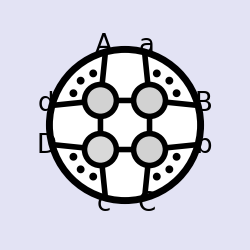
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
SetDirectory[NotebookDirectory[]];
<<"loop_amplitudes.m"
```

```mathematica
Zs={{Sqrt[F1]S1,0,1/(Sqrt[F1]T1),T1/Sqrt[F1]},{1,0,0,0},{-S2/Sqrt[F2],0,0,S2/Sqrt[F2]},{-S2/Sqrt[F2],Sqrt[F2]/T2,-Sqrt[F2]/T2,S2/Sqrt[F2]+Sqrt[F2]/T2+Sqrt[F2] T2},{0,1/(Sqrt[F2]S2)+Sqrt[F2]/T2,-Sqrt[F2]/T2,Sqrt[F2]/T2},{0,1,0,0},{0,Sqrt[F1]/S1,1/(Sqrt[F1]T1),0}};
```

```mathematica
R1111=evaluate@superComponent[{1,2,3,4},{},{},{},{},{},{}]@ratioIntegral[7,1]//Map[Simplify,#,{1}]&;
```

```mathematica
num={S1->3,S2->4,F1->1/5,F2->1/6,T1->1/70,T2->1/80};
```

```mathematica
R1111/.num//Simplify//N[#,10]&
```

-0.2440772457

## T expansion

```mathematica
ListR1111=Reverse[List@@R1111];
```

```mathematica
ClearAll[series];
series[X_]:=series[X]=(Series[Simplify@X,{T1,0,4}]/.C_Floor->0//Normal//Series[#,{T2,0,4}]&//Normal)/.C_Floor->0/.Log[a_]:>PowerExpand@Log@Factor@a/.c_PolyLog:>FullSimplify[c];
```

```mathematica
ListListR1111=Monitor[Table[series@ListR1111⟦j⟧,{j,Length[ListR1111]}],{j,Length[ListR1111]}];
```

```mathematica
almost=Collect[#,{T1,T2,Log[_],PolyLog[2,_]},s]&/@ListListR1111;
```

```mathematica
prefactors=Reverse@Union@Cases[almost,c_s,∞];
```

```mathematica
prefactorS=Monitor[Table[prefactors⟦j⟧/.s[a_]:>a//Factor,{j,Length[prefactors]}],{j,Length[prefactors]}];
```

```mathematica
almost2=almost/.Inner[Rule,prefactors,prefactorS,List]//Total//Collect[#,{T1,T2,F1,F2},Collect[#,Log[_]|PolyLog[2,_],f]&]&;
```

```mathematica
fs=Reverse@Union@Cases[almost2,c_f,∞];
```

```mathematica
fsS=Monitor[Table[fs⟦j⟧/.f[a_]:>a//Factor//Simplify,{j,Length[fs]}],{j,Length[fs]}];
```

```mathematica
finalT1T2=almost2/.Inner[Rule,fs,fsS,List]/.f[a_]:>a;
```

```mathematica
finalT1T2>>(NotebookDirectory[]<>"R1111T1T2toFourthPower.txt");
```

```mathematica
finalT1T2/.num//N[#,20]&
```

-0.24407711090345159276

## S expansion

```mathematica
R1111finalGs=finalT1T2//Collect[#,{T1,T2,Log[T1],Log[T2],F1,F2,Log[_],PolyLog[2,_]},G]&;
```

```mathematica
Gs2=Cases[R1111finalGs,G[a_],∞]//Union//Reverse;
```

```mathematica
Gs2Expanded=Monitor[Table[Gs2⟦j⟧/.G[a_]:>a//Series[#,{S1,∞,25}]&//Series[#,{S2,∞,25}]&//Normal//ExpandAll,{j,Length[Gs2]}],{j,Length[Gs2]}];
```

```mathematica
logspolys=Cases[finalT1T2,Log[_]|PolyLog[2,_],∞]//Union//Reverse;
```

```mathematica
logspolysExpanded=Monitor[Table[logspolys⟦j⟧/.PolyLog[2,x_]:>(-PolyLog[2,1-x]- Log[x]Log[1-x]+π^2/6)/;Abs[x-1/.{S1->10000,S2->10000}]<1/10//Series[#,{S1,∞,25}]&//Series[#,{S2,∞,25}]&//Normal//ExpandAll,{j,Length[logspolys]}],{j,Length[logspolys]}];
```

```mathematica
R1111finalS1S2=R1111finalGs/.Inner[Rule,Gs2,Gs2Expanded,List]/.Inner[Rule,logspolys,logspolysExpanded,List];
```

```mathematica
R1111finalS1S2log=R1111finalS1S2/.Log[1/S2]->-LogS2/.Log[1/S1]->-LogS1/.Log[T1]->LogT1/.Log[T2]->LogT2//Collect[#,{T1,T2,F1,F2,LogT1,LogT2},F]&;
```

```mathematica
Fs=Cases[R1111finalS1S2log,F[a_],∞]//Union//Reverse;
```

```mathematica
FsExpanded=Monitor[Table[Fs⟦j⟧/.F[a_]:>a//Series[#,{S1,∞,20}]&//Normal//Series[#,{S2,∞,20}]&//Normal//ExpandAll,{j,Length[Fs]}],{j,Length[Fs]}];
```

```mathematica
R1111finalS1S2Expanded=R1111finalS1S2log/.Inner[Rule,Fs,FsExpanded,List]/.LogS1->Log[S1]/.LogS2->Log[S2]/.LogT1->Log[T1]/.LogT2->Log[T2];
```

```mathematica
R1111finalS1S2Expanded>>(NotebookDirectory[]<>"R1111T1T2toFourthPowerS1S2toOrder20.txt")
```

```mathematica
R1111finalS1S2Expanded/.num//N[#,20]&
```

-0.24407711083513985054